```mathematica
Plot3D[(CP/Cd)^(1/3),{CP, 0,1000},{Cd,0,1},AxesLabel->{"Critical Power (W)","Drag Coefficent","Max Velocity (m/s)"}]
```

-Graphics3D-

P = C_d v^3 + mg sin (theta) v

```mathematica
c= 1
m = 70
g = 9.8
Plot3D[c v^3+m g Sin[θ] v, {v, -30,30},{θ,-π/6,π/6},AxesLabel->{"Velocity (m/s)","Theta (rad)", "Power (W)"}]
```

1

70

9.8

-Graphics3D-

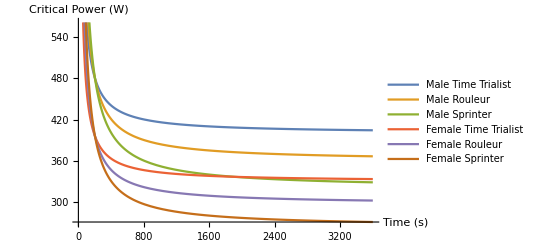

```mathematica
MTT[t_]:=16200(1/t)+400
MR[t_] := 24300 (1/t)+360
MS[t_] := 32400 (1/t)+320

FTT[t_] := 13365 (1/t)+330
FR[t_] := 20047.5(1/t)+297
FS[t_] := 26730 (1/t)+264

pc = Plot[{MTT[t],MR[t],MS[t],FTT[t],FR[t],FS[t]},{t, 5, 3600},ScalingFunctions->{"Linear","Linear"},PlotLegends->{"Male Time Trialist", "Male Rouleur","Male Sprinter","Female Time Trialist","Female Rouleur", "Female Sprinter"},AxesLabel->{"Time (s)", "Critical Power (W)"}]
```

```mathematica
Export["C:\\Users\\madie\\mcm-2022\\power-curve.png",pc]
```

C:\Users\madie\mcm-2022\power-curve.png

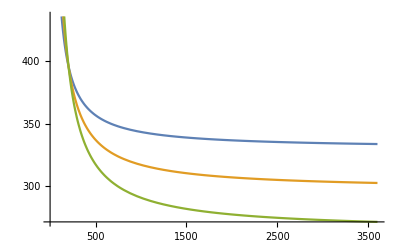

```mathematica
Plot[{FTT[t],FR[t],FS[t]},{t, 5, 3600},ScalingFunctions->{"Linear","Linear"}]
```